# Moving point heat source

In this short notice we explore solution to moving heat source given by the paper “Solutions for modelling moving heat sources in semi-infinite medium and applications to laser material processing”
by M.Van Elsen, M.Baelmans, P.Mercelis, J.-P.Kruth  doi:10.1016/j.ijheatmasstransfer.2007.02.044.

Moving point heat source in 3 D semi-inifite body is described by Carslaw and Jaeger:
k  conductivity (W/mK)
T0   room temperature (K)
Tm melting temperature (K)
V scan speed (m/s)
x coordinate along scanning direction (m)
y coordinate perpendicular to scanning direction (m)
z coordinate in depth (m)
P laser power (W)

Values of thermal parameters for Ti - 6 Al - 4 V

In the paper by M.Van Elsen the Eq.(5) there is type error it should be:
θ = P_L/(2 π k R(T-T_o))exp(-V(R+x)/2κ)

```mathematica
Tm=1933;
T0=293;
k=6.0;
κ =2.4 10^-6;
```

```mathematica
θ[P_,κ_,V_,x_,y_,z_]:= P/(2 π k √(x^2+y^2+z^2)(Tm-T0)) Exp[-V(√(x^2+y^2+z^2)+x)/(2 κ)];
```

Result for moving point source

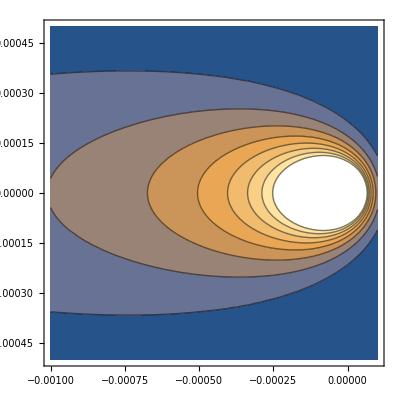

```mathematica
ContourPlot[θ[25.0,κ,0.05,x,y,0.0],{x,-10 10^-4,1 10^-4},{y,-5 10^-4,5 10^-4}]
```

These are results for Uniform moving heat source:
The solution is given by M.Van Elsen et al. International Journal of Heat and mass transfer.
50 (2007) 4872-4882.

Definition of the Fourier number:
Fo = (diffusive transport rate)/(storage rate)=αt/L^2

The additional material parameters for uniform source term are:

```mathematica
ρ = 4450; (*density in kg/m^3 *)
cp = 546;(* specific heat in J/kg K *)
k = 6 ; (*conductivity W/m K *)
ah =ch = 0.00015; (* laser dimension in m *)
bh = 0.000005; (* laser dimension in m *)
```

```mathematica
Fos[κ_,s_,t_]:=(κ t)/s^2
```

```mathematica
η [P_,ρ_,cp_,ah_,bh_,ch_,Tm_,To_,t_]:=ρ cp ah bh ch (Tm-To)/(P t);
```

```mathematica
Erfh[κ_,x_,s_,tp_]:=Erf[(√Fos[κ,s,tp])/2(x/s-1)]-Erf[(√Fos[κ,s,tp])/2(x/s+1)]
θunif[P_,κ_,V_,x_,y_,z_,t_]:=-1/(2^5 η[P,ρ,cp,ah,bh,ch,Tm,T0,t])NIntegrate[Erfh[x+V(t-tp),ch,tp]*Erfh[y,ah,tp]*Erfh[z,bh,tp], {tp,0,t}]
```

#### in original paper the Fo is seems defined as s^2/κ(t-t')

```mathematica
mErfh[κ_,x_,s_,t_,tp_]:=Erf[(x-s)/(√(4 κ(t-tp)))]-Erf[(x+s)/(√(4 κ(t-tp)))];
```

```mathematica
mθ[P_,κ_,V_,x_,y_,z_,t_]:=-P/(2^5 ρ ah bh ch (Tm-T0))NIntegrate[mErfh[κ,x+V(t-tp),ch,t,tp] *mErfh[κ,y,ah,t,tp]*mErfh[κ,z,bh,t,tp], {tp,0,t},MinRecursion-> 2]
```

```mathematica
funx[x_,y_,z_,time_]:=-25/(2^5 ρ cp ah bh ch (Tm-T0))NIntegrate[mErfh[κ,x+0.05(time-tp),ch,time,tp]*mErfh[κ,y,ah,time,tp]*mErfh[κ,z,bh,time,tp] ,{tp,0,time},MinRecursion-> 2]
```

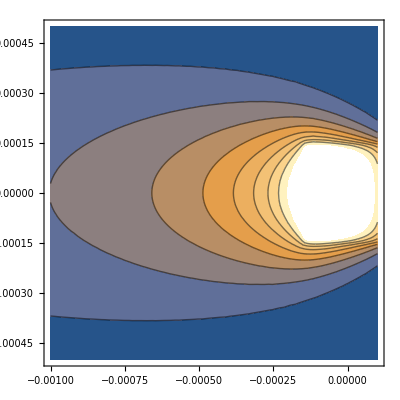

```mathematica
ContourPlot[funx[x,y,0.0,10],{x,-10 10^-4,1 10^-4},{y,-5 10^-4,5 10^-4}]
```

3d plot of the uniform moving source:

```mathematica
Plot3D[funx[x,y,0.0,10],{x,-10 10^-4,1 10^-4},{y,-5 10^-4,5 10^-4},PlotRange->{0,3}]
```

-Graphics3D-

Some specific cross sections of this solutions are:

```mathematica
max = FindMaximum[funx[x,0.0,0.0,10],{x,-10 10^-4,1 10^-4}]
```

NIntegrate::inumr: The integrand 4 Erf[0.00161374/(√(10-tp))] Erf[0.0484123/(√(10-tp))] (Erf[(322.749 (-0.00015+0.05 (10+Times[«2»])+x))/(√(10-tp))]-Erf[(322.749 (0.00015+0.05 Plus[«2»]+x))/(√(10+Times[«2»]))]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,2.5}}.

```mathematica
x /. Last[max]
```

-0.000101099

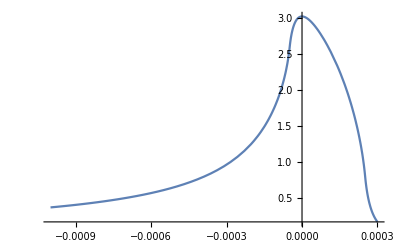

```mathematica
Plot[funx[x-0.00010109930098839564,0,0.0,10],{x,-10 10^-4,3 10^-4}, PlotRange->All]
```

and for x=0 we have:

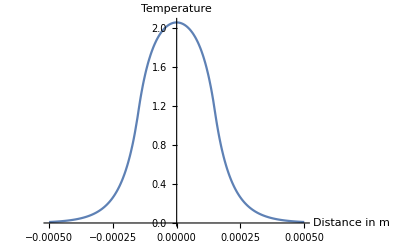

```mathematica
Plot[funx[0,y,0.0,10],{y,-5 10^-4,5 10^-4}, PlotRange->All,AxesLabel->{"Distance in m", "Temperature"}]
```